# 隣接行列とそのEigen

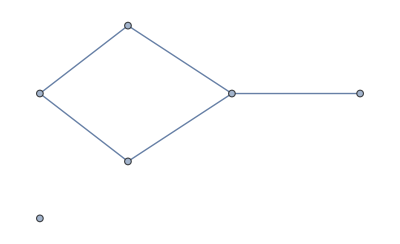

```mathematica
rg=RandomGraph[{6,5}]
```

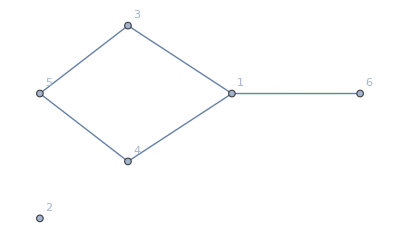

```mathematica
Graph[rg,VertexLabels->Automatic]
```

```mathematica
AdjacencyMatrix[rg]//Normal
```

{{0,0,1,1,0,1},{0,0,0,0,0,0},{1,0,0,0,1,0},{1,0,0,0,1,0},{0,0,1,1,0,0},{1,0,0,0,0,0}}

```mathematica
ev=Eigenvectors[KirchhoffMatrix[rg]]//N
```

{{-3.48119,0.,2.07816,2.07816,-1.67513,1.},{-1.68889,0.,-0.762714,-0.762714,2.21432,1.},{0.,0.,-1.,1.,0.,0.},{0.170086,0.,-0.315449,-0.315449,-0.539189,1.},{1.,0.,1.,1.,1.,1.},{0.,1.,0.,0.,0.,0.}}

```mathematica
ep=Transpose[ev]
```

{{-3.48119,-1.68889,0.,0.170086,1.,0.},{0.,0.,0.,0.,0.,1.},{2.07816,-0.762714,-1.,-0.315449,1.,0.},{2.07816,-0.762714,1.,-0.315449,1.,0.},{-1.67513,2.21432,0.,-0.539189,1.,0.},{1.,1.,0.,1.,1.,0.}}

```mathematica
m={{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,0,0,0},{0,0,0,0,1,1},{0,1,0,0,0,0}}
```

{{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,0,0,0},{0,0,0,0,1,1},{0,1,0,0,0,0}}

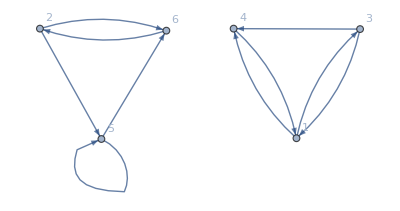

```mathematica
g=AdjacencyGraph[m,VertexLabels->Automatic]
```

```mathematica
ev=Eigenvectors[m]
```

{{0,1/2 (1+√5),0,0,1/2 (1+√5),1},{1/2 (1+√5),0,1/2 (1+√5),1,0,0},{-1,0,0,1,0,0},{0,1/2 (1-√5),0,0,1/2 (1-√5),1},{1/2 (1-√5),0,1/2 (1-√5),1,0,0},{0,0,0,0,-1,1}}

```mathematica
ep=Transpose[ev]
```

{{0,1/2 (1+√5),-1,0,1/2 (1-√5),0},{1/2 (1+√5),0,0,1/2 (1-√5),0,0},{0,1/2 (1+√5),0,0,1/2 (1-√5),0},{0,1,1,0,1,0},{1/2 (1+√5),0,0,1/2 (1-√5),0,-1},{1,0,0,1,0,1}}

```mathematica
ep2=Map[#[[1;;2]]&,ep]//N
```

{{0.,1.61803},{1.61803,0.},{0.,1.61803},{0.,1.},{1.61803,0.},{1.,0.}}

```mathematica
MapIndexed[Text[]]
```